```mathematica
Clear[c, eV,u,m,m3,ms,s,vf,kf,Nf]
m=1;s=1;eV=1;
c=2.99792458 10^8 m s^-1;
hbar=6.582119569 10^-16 eV s;
(*π=3.1415926;*)
u=9.3149410242 10^8 eV c^-2;
m3=3.016293 u;
ms=5.02 m3;
vf=36.53 m s^-1;

kf=(vf ms)/hbar

Nf=(ms kf)/(π^2 hbar^2)
```

8.70963×10^9

3.19657×10^32

0.0000861733

0.002339

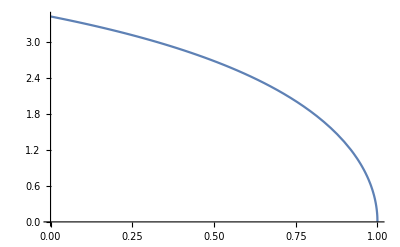

3.42482

```mathematica
Clear[t,T,Tc,kb,c2,c4,c5,c245,Δ2,Δ,fGLReduced,αReduced,βReduced]
(**pressure is 24 bar**)
(*c2 = -0.07;c4=-0.72;c5=0.04;*)
c2 = -0.1306;c4=-0.2795;c5=-0.3280;
c245=c2+c4+c5;
kb=8.617333262145 10^-5(**eV.K^-1*)
Tc=2.339 10^-3(*mK, kevin*)
(*********)
αReduced=1/3 (t-1);
βReduced=(1/(30 π^2) (7/8 Zeta[3])) (2+t c245);
Δ=√(-αReduced/(4 βReduced));
Plot[Δ,{t,0,1},PlotLegends->"Placeholder"]
Δ/.t->0.0
```

0.0000861733

0.002339

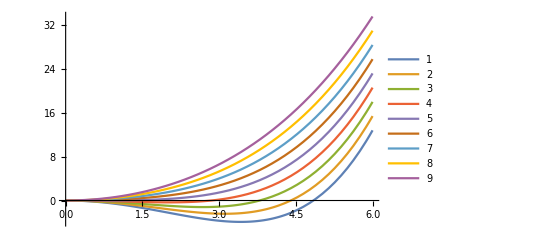

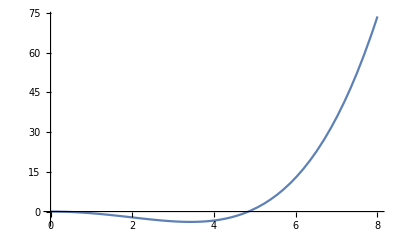

```mathematica
Clear[t,T,Tc,kb,c2,c4,c5,c245,Δ2,Δ,fGLReduced,αRe,βRe]
(**pressure is 24 bar**)
(*c2 = -0.07;c4=-0.72;c5=0.04;*)
c2 = -0.1306;c4=-0.2795;c5=-0.3280;
c245=c2+c4+c5;
kb=8.617333262145 10^-5(**eV.K^-1*)
Tc=2.339 10^-3(*mK, kevin*)
(*********)
αRe=1/3 (t-1);
βRe=(1/(30 π^2) (7/8 Zeta[3])) (2+t c245);
fGLReduced=2 Δ^2 αRe+4 Δ^4 βRe;
Plot[{fGLReduced/.t->0,fGLReduced/.t->0.25,fGLReduced/.t->0.5,fGLReduced/.t->0.75,fGLReduced/.t->1,fGLReduced/.t->1.25,fGLReduced/.t->1.5,fGLReduced/.t->1.75,fGLReduced/.t->2.0},{Δ,0,6},PlotLegends->"Placeholder"]
Plot[{fGLReduced/.t->0.0},{Δ,0,8},PlotLegends->"Placeholder"]
```

0.0000861733

0.002339

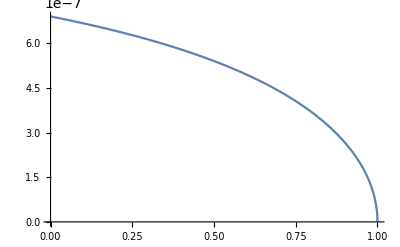

6.90306×10^-7

```mathematica
Clear[t,T,Tc,kb,c2,c4,c5,c245,Δ2,Δ,fGLReduced,αReduced,βReduced]
(**pressure is 24 bar**)
(*c2 = -0.07;c4=-0.72;c5=0.04;*)
c2 = -0.1306;c4=-0.2795;c5=-0.3280;
c245=c2+c4+c5;
kb=8.617333262145 10^-5(**eV.K^-1*)
Tc=2.339 10^-3(*mK, kevin*)
(*********)
αReduced=1/3 (t-1);
βReduced=(1/(30 π^2 kb^2 Tc^2) (7/8 Zeta[3])) (2+t c245);
Δ=√(-αReduced/(4 βReduced));
Plot[Δ,{t,0,1},PlotLegends->"Placeholder"]
Δ/.t->0.0
```

8.70963×10^9

3.19657×10^32

0.0000861733

0.002339

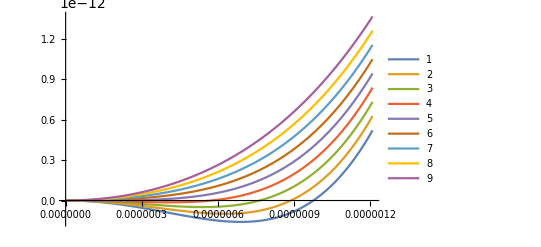

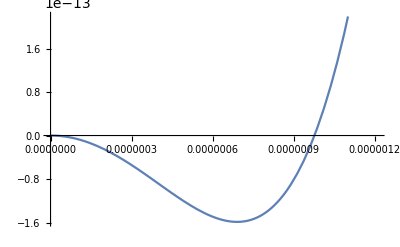

```mathematica
Clear[α,β,c, eV,u,m,m3,ms,s,vf,kf,Nf,t,T,Tc,kb,c2,c4,c5,c245,Δ2,Δ,αRe,βRe]
m=1;s=1;eV=1;
c=2.99792458 10^8 m s^-1;
hbar=6.582119569 10^-16 eV s;
(*π=3.1415926;*)
u=9.3149410242 10^8 eV c^-2;
m3=3.016293 u;
ms=5.02 m3;
vf=36.53 m s^-1;
kf=(vf ms)/hbar
Nf=(ms kf)/(π^2 hbar^2)
(**pressure is 24 bar**)
c2 = -0.1306;c4=-0.2795;c5=-0.3280;
c245=c2+c4+c5;
kb=8.617333262145 10^-5(**eV.K^-1*)
Tc=2.339 10^-3(*mK, kevin*)
(*********)
αRe=1/3 (t-1);
βRe=(1/(30 π^2 kb^2 Tc^2) (7/8 Zeta[3])) (2+t c245);
fGLReduced=2 Δ^2 αRe+4 Δ^4 βRe;
Plot[{fGLReduced/.t->0,fGLReduced/.t->0.25,fGLReduced/.t->0.5,fGLReduced/.t->0.75,fGLReduced/.t->1,fGLReduced/.t->1.25,fGLReduced/.t->1.5,fGLReduced/.t->1.75,fGLReduced/.t->2.0},{Δ,0,6 kb Tc},PlotLegends->"Placeholder"]
Plot[{fGLReduced/.t->0.0},{Δ,0,6 kb Tc},PlotLegends->"Placeholder"]
```

8.70963×10^9

3.19657×10^32

0.0000861733

0.002339

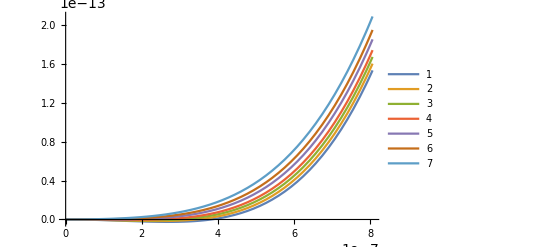

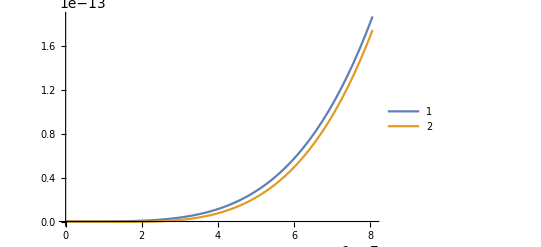

```mathematica
Clear[α,β,c, eV,u,m,m3,ms,s,vf,kf,Nf,t,T,Tc,kb,c2,c4,c5,c245,Δ2,Δ,αRe,βRe]
m=1;s=1;eV=1;
c=2.99792458 10^8 m s^-1;
hbar=6.582119569 10^-16 eV s;
(*π=3.1415926;*)
u=9.3149410242 10^8 eV c^-2;
m3=3.016293 u;
ms=5.02 m3;
vf=36.53 m s^-1;
kf=(vf ms)/hbar
Nf=(ms kf)/(π^2 hbar^2)
(**pressure is 24 bar**)
c2 = -0.1306;c4=-0.2795;c5=-0.3280;
c245=c2+c4+c5;
kb=8.617333262145 10^-5(**eV.K^-1*)
Tc=2.339 10^-3(*mK, kevin*)
(*********)
αRe=1/3 (T/Tc-1);
βRe=(1/(30 π^2 kb^2 Tc^2) (7/8 Zeta[3])) (2+T/Tc c245);
fGLReduced=2 Δ^2 αRe+4 Δ^4 βRe;
Plot[{fGLReduced/.T->2.1 10^-3,fGLReduced/.T->2.15 10^-3,fGLReduced/.T->2.2 10^-3,fGLReduced/.T->2.25 10^-3,fGLReduced/.T->2.33 10^-3,fGLReduced/.T->2.4 10^-3,fGLReduced/.T->2.5 10^-3},{Δ,0,4 kb Tc},PlotLegends->"Placeholder"]
Plot[{fGLReduced/.T->2.339 10^-3,fGLReduced/.T->2.25 10^-3},{Δ,0,4 kb Tc},PlotLegends->"Placeholder"]
```

0.0000861733

0.002483

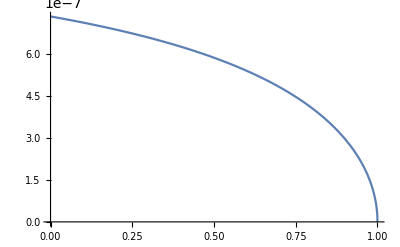

7.32804×10^-7

```mathematica
Clear[t,T,Tc,kb,c2,c4,c5,c245,Δ2,Δ,fGLReduced,αReduced,βReduced]
(**pressure is 32 bar**)
(*c2 = -0.07;c4=-0.72;c5=0.04;*)
c2 = -0.1583;c4=-0.3388;c5=-0.3717;
c245=c2+c4+c5;
kb=8.617333262145 10^-5(**eV.K^-1*)
Tc=2.483 10^-3(*mK, kevin*)
(*********)
αReduced=1/3 (t-1);
βReduced=(1/(30 π^2 kb^2 Tc^2) (7/8 Zeta[3])) (2+t c245);
Δ=√(-αReduced/(4 βReduced));
Plot[Δ,{t,0,1},PlotLegends->"Placeholder"]
Δ/.t->0.0
```

8.70963×10^9

3.19657×10^32

0.0000861733

0.002463

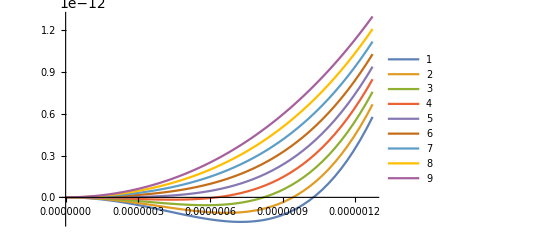

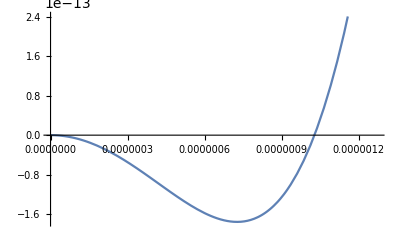

```mathematica
Clear[α,β,c, eV,u,m,m3,ms,s,vf,kf,Nf,t,T,Tc,kb,c2,c4,c5,c245,Δ2,Δ,αRe,βRe]
m=1;s=1;eV=1;
c=2.99792458 10^8 m s^-1;
hbar=6.582119569 10^-16 eV s;
(*π=3.1415926;*)
u=9.3149410242 10^8 eV c^-2;
m3=3.016293 u;
ms=5.02 m3;
vf=36.53 m s^-1;
kf=(vf ms)/hbar
Nf=(ms kf)/(π^2 hbar^2)
(**pressure is 32 bar**)
c2 = -0.1583;c4=-0.3388;c5=-0.3717;
c245=c2+c4+c5;
kb=8.617333262145 10^-5(**eV.K^-1*)
Tc=2.463 10^-3(*mK, kevin*)
(*********)
αRe=1/3 (t-1);
βRe=(1/(30 π^2 kb^2 Tc^2) (7/8 Zeta[3])) (2+t c245);
fGLReduced=2 Δ^2 αRe+4 Δ^4 βRe;
Plot[{fGLReduced/.t->0,fGLReduced/.t->0.25,fGLReduced/.t->0.5,fGLReduced/.t->0.75,fGLReduced/.t->1,fGLReduced/.t->1.25,fGLReduced/.t->1.5,fGLReduced/.t->1.75,fGLReduced/.t->2.0},{Δ,0,6 kb Tc},PlotLegends->"Placeholder"]
Plot[{fGLReduced/.t->0.0},{Δ,0,6 kb Tc},PlotLegends->"Placeholder"]
```

0.0000861733

0.001934

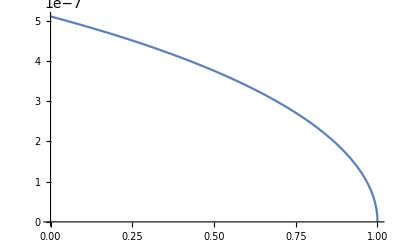

5.1052×10^-7

```mathematica
Clear[t,T,Tc,kb,c2,c4,c5,c12,c345,Δ2,Δ,fBGLReduced,αReduced,βBReduced]
(**pressure is 12 bar**)
c1 = -0.0254;c2 = -0.0861;c3 = -0.0233;c4=-0.1508;c5=-0.2503;
c12 = c1 + c2;
c345=c3+c4+c5;
kb=8.617333262145 10^-5(**eV.K^-1*)
Tc=1.934 10^-3(*mK, kevin*)
(*********)
αReduced=1/3 (t-1);
βBReduced=(1/(30 π^2 kb^2 Tc^2) (7/8 Zeta[3])) (3 (1+t c12)+(2+t c345));
Δ=√(-αReduced/(2 βBReduced));
Plot[Δ,{t,0,1},PlotLegends->"Placeholder"]
Δ/.t->0.0
```

8.70963×10^9

3.19657×10^32

0.0000861733

0.001934

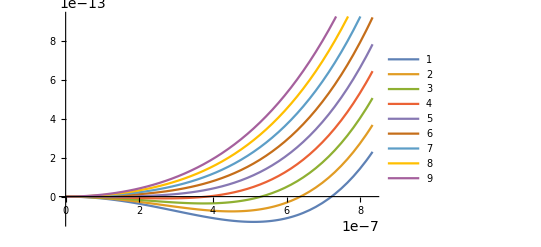

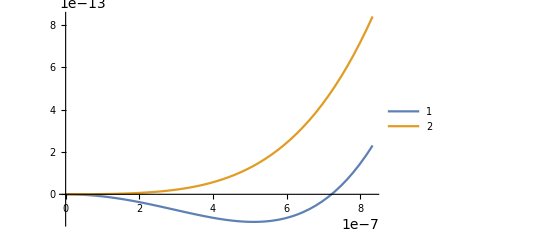

```mathematica
Clear[α,β,c, eV,u,m,m3,ms,s,vf,kf,Nf,t,T,Tc,kb,c1,c2,c3,c4,c5,c12,c345,Δ2,Δ,αReduced,βBReduced]
m=1;s=1;eV=1;
c=2.99792458 10^8 m s^-1;
hbar=6.582119569 10^-16 eV s;
(*π=3.1415926;*)
u=9.3149410242 10^8 eV c^-2;
m3=3.016293 u;
ms=5.02 m3;
vf=36.53 m s^-1;
kf=(vf ms)/hbar
Nf=(ms kf)/(π^2 hbar^2)
(**pressure is 32 bar**)
c1 = -0.0254;c2 = -0.0861;c3 = -0.0233;c4=-0.1508;c5=-0.2503;
c12 = c1 + c2;
c345=c3+c4+c5;
kb=8.617333262145 10^-5(**eV.K^-1*)
Tc=1.934 10^-3(*mK, kevin*)
(*********)
αReduced=1/3 (t-1);
βBReduced=(1/(30 π^2 kb^2 Tc^2) (7/8 Zeta[3])) (3 (1+t c12)+(2+t c345));
fBGLReduced=3 Δ^2 αReduced+3 Δ^4 βBReduced;
Plot[{fBGLReduced/.t->0,fBGLReduced/.t->0.25,fBGLReduced/.t->0.5,fBGLReduced/.t->0.75,fBGLReduced/.t->1,fBGLReduced/.t->1.25,fBGLReduced/.t->1.5,fBGLReduced/.t->1.75,fBGLReduced/.t->2.0},{Δ,0,5 kb Tc},PlotLegends->"Placeholder"]
Plot[{fBGLReduced/.t->0.0,fBGLReduced/.t->1.1},{Δ,0,5 kb Tc},PlotLegends->"Placeholder"]
```